v2: updated version following notes, plus Mean-field
v3: mean-field (more) + ϵ implementation

### Set Options

Automating good looking plots

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

```mathematica
SetOptions[ ListContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ ListDensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

```mathematica
SetOptions[ ContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ DensityPlot,Frame-> True,LabelStyle->{FontFamily->"CMU Serif",FontSize->24,Black},ImageSize->Medium];
```

### Parameters

Lattice vectors, and basis vectors

```mathematica
a1 = {1,0};a2 ={0,1};τA = {1/2,0};τB = {0,0}; τC = {0,1/2};τvec = {τA,τB, τC};
```

Reciprocal lattice vectors

```mathematica
LatMat = {a1,a2}; 
ReciLatMat = 2π Inverse[LatMat]†;
b1 = ReciLatMat[[1]] ;b2 = ReciLatMat[[2]];
```

```mathematica
δf=N[1/(2√2)];
```

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
rSpan[range_]:=N[Flatten[Table[i*a1+j*a2,{i,-range,range},{j,-range,range}],1]];
```

```mathematica
inp[a_,b_]:= Conjugate[a].b;
```

We will play around with k-range and range to check for convergence

```mathematica
Fermi[β_,x_]:=Chop[N[ 1/(1+ Exp[ β x])]];DFermi[β_,x_] :=D[ Fermi[β,x1],x1]/.{x1-> x};
```

### Bloch Hamiltonian

```mathematica
MatX[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δx)(IdentityMatrix[2]+ I λR PauliMatrix[2] +I λD PauliMatrix[1]) + (1-δx)Exp[I k.a1](IdentityMatrix[2]- I λR PauliMatrix[2] -I λD PauliMatrix[1])];
```

```mathematica
MatY[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δy)(IdentityMatrix[2]- I λR PauliMatrix[1] +I λD PauliMatrix[2]) + (1-δy)Exp[I k.a2](IdentityMatrix[2]+ I λR PauliMatrix[1] -I λD PauliMatrix[2])];
```

```mathematica
Clear[hamLieb];hamLieb[bsp_,k_] := hamLieb[bsp,k] = Module[{λ = bsp[[1]], δ = bsp[[2]], ϵ = bsp[[3]]},Module[ {mx = MatX[λ,δ,k],my = MatY[λ,δ,k] },ArrayFlatten[ {{-ϵ IdentityMatrix[2],mx,my},{mx†,0,0},{my†,0,0}} ]]];
```

```mathematica
Block[ {bsp ={RandomReal[{0,1},2],RandomReal[1,2],0.1},k=RandomReal[2π,2]},hamLieb[bsp,k]]//MatrixForm
```

(-0.1 | 0. | 1.69152+0.658 ⅈ | 0.848709+0.0178491 ⅈ | 0.553437+0.678158 ⅈ | 0.78855-1.54387 ⅈ
0. | -0.1 | 0.100854+0.842885 ⅈ | 1.69152+0.658 ⅈ | -1.63886-0.565211 ⅈ | 0.553437+0.678158 ⅈ
1.69152-0.658 ⅈ | 0.100854-0.842885 ⅈ | 0 | 0 | 0 | 0
0.848709-0.0178491 ⅈ | 1.69152-0.658 ⅈ | 0 | 0 | 0 | 0
0.553437-0.678158 ⅈ | -1.63886+0.565211 ⅈ | 0 | 0 | 0 | 0
0.78855+1.54387 ⅈ | 0.553437-0.678158 ⅈ | 0 | 0 | 0 | 0)

```mathematica
Clear[EnerLieb];EnerLieb[bsp_,k_] := EnerLieb[bsp,k]= Chop[  N[Sort[Eigenvalues[hamLieb[bsp,k] ]]] ];
Clear[ULieb];ULieb[bsp_,k_] :=ULieb[bsp,k]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[ hamLieb[bsp,k] ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
Block[ {bsp ={RandomReal[{0,1},2],RandomReal[1,2],0.1},k=RandomReal[2π,2]},ULieb[bsp,k]]//MatrixForm
```

(-0.253345+0.434978 ⅈ | 0.487158-0.129294 ⅈ | 0 | 0 | 0.479349-0.127222 ⅈ | -0.249933+0.429119 ⅈ
-0.484614+0.13616 ⅈ | -0.439868-0.246081 ⅈ | 0 | 0 | -0.432817-0.242137 ⅈ | -0.478086+0.134326 ⅈ
-0.128406-0.221877 ⅈ | -0.463199-0.0745519 ⅈ | -0.429662-0.213045 ⅈ | 0.331273+0.282077 ⅈ | 0.470744+0.0757664 ⅈ | 0.13016+0.224906 ⅈ
0.341281-0.288176 ⅈ | 0.0124346+0.174529 ⅈ | -0.34545+0.439321 ⅈ | -0.392981+0.257817 ⅈ | -0.0126372-0.177373 ⅈ | -0.345941+0.292111 ⅈ
0.206791-0.0448018 ⅈ | -0.405312+0.233143 ⅈ | 0.673763-0.0608898 ⅈ | -0.0729731-0.0423247 ⅈ | 0.411915-0.236941 ⅈ | -0.209614+0.0454135 ⅈ
0.428035 | 0.150204 | 0 | 0.763329 | -0.152651 | -0.433879)

#### Plot Band Structure

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
PlotDispData[bsp_] := Table[ EnerLieb[bsp,k]  ,{k,kCut} ];
```

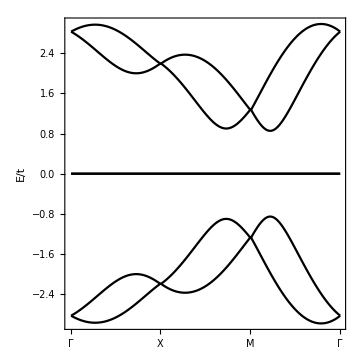

```mathematica
Block[ {bsp={{0.0,0.45},{0.0,0.0},0}},ListPlot[Table[ PlotDispData[bsp][[All,i]],{i,1,6}],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Mean Field Theory

Here nup, ndn, splus and sdown are all 3 vectors (for A, B, C)

Follow Eq. 5 of ref https://arxiv.org/pdf/2110.03813.pdf

```mathematica
Clear[HamMFU];HamMFU[nup_, ndn_, spls_, smns_]:= HamMFU[nup,ndn, spls, smns] = {{ ndn[[1]], - smns[[1]],0,0,0,0},{-spls[[1]], nup[[1]],0,0,0,0},{0,0, ndn[[2]], - smns[[2]],0,0},{0,0,-spls[[2]], nup[[2]],0,0},{0,0,0,0, ndn[[3]], - smns[[3]]},{0,0,0,0,-spls[[3]], nup[[3]]}} ;
```

```mathematica
Clear[HamMFUcl];HamMFUcl[nup_, ndn_, spls_, smns_]:= HamMFUcl[nup,ndn, spls, smns] = KroneckerProduct[ArrayFlatten[ Table[ If[i==j, smns[[i]] spls[[i]] -  nup[[i]] ndn[[i]], 0.0] ,{i,1,3},{j,1,3}]],IdentityMatrix[2]] ;
```

```mathematica
Clear[HamMFull];HamMFull[bsp_,nup_, ndn_, spls_, smns_,k_,U_]:= HamMFull[bsp,nup,ndn, spls, smns,k,U]= hamLieb[bsp,k] +U HamMFU[nup,ndn, spls, smns];
```

```mathematica
IJMat[i_,j_,N_]:= ArrayFlatten[ Table[ If[i1==i&&j1==j,1,0],{i1,1,N},{j1,1,N}]];
```

```mathematica
Clear[EnerMF];EnerMF[bsp_,nup_, ndn_, spls_, smns_,k_,U_] := EnerMF[bsp,nup,ndn, spls, smns,k,U]= Chop[  N[Sort[Eigenvalues[HamMFull[bsp,nup,ndn, spls, smns,k,U] ]]] ];
```

```mathematica
Clear[ULiebMF];ULiebMF[bsp_,nup_, ndn_, spls_, smns_,k_,U_] :=ULiebMF[bsp,nup,ndn, spls, smns,k,U]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[HamMFull[bsp,nup,ndn, spls, smns,k,U]  ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
Clear[nupMF];nupMF[bsp_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=nupMF[bsp,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Module[{um = ULiebMF[bsp,nup,ndn, spls, smns,k,U]},Table[ Fermi[β, EnerMF[bsp,nup,ndn, spls, smns,k,U][[band]] -μ](um†.IJMat[2orb,2orb,6].um)[[band,band]],{orb,1,3}]],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[ndnMF];ndnMF[bsp_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=ndnMF[bsp,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Module[{um = ULiebMF[bsp,nup,ndn, spls, smns,k,U]},Table[ Fermi[β, EnerMF[bsp,nup,ndn, spls, smns,k,U][[band]] -μ](um†.IJMat[2orb-1,2orb-1,6].um)[[band,band]],{orb,1,3}]],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[splsMF];splsMF[bsp_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=splsMF[bsp,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[bsp,nup,ndn, spls, smns,k,U][[band]] -μ]Module[{um = ULiebMF[bsp,nup,ndn, spls, smns,k,U]},Table[ -Fermi[β, EnerMF[bsp,nup,ndn, spls, smns,k,U][[band]] -μ](um†.IJMat[2orb,2orb-1,6].um)[[band,band]],{orb,1,3}]],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[smnsMF];smnsMF[bsp_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=smnsMF[bsp,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Module[{um = ULiebMF[bsp,nup,ndn, spls, smns,k,U],zr = {0,0,0}},Table[ -Fermi[β, EnerMF[bsp,nup,ndn, spls, smns,k,U][[band]] -μ](um†.IJMat[2orb-1,2orb,6].um)[[band,band]],{orb,1,3}]],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[NumEq];NumEq[bsp_,nup_, ndn_, spls_, smns_,U_,μ_,β_,krange_] :=NumEq[bsp,nup,ndn, spls, smns,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[bsp,nup,ndn, spls, smns,k,U][[band]] -μ],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[FindMu];FindMu[bsp_,nup_, ndn_, spls_, smns_,U_,fil_,β_,krange_] :=FindMu[bsp,nup,ndn, spls, smns,U,fil,β,krange]=μ/.FindRoot[ NumEq[bsp,nup,ndn, spls, smns,U,μ,β,krange]-fil,{μ,-10,10},Evaluated->False, MaxIterations->20,PrecisionGoal->3];
```

```mathematica
Clear[ItrFnMF];ItrFnMF[bsp_,U_,fil_,β_,krange_]:= ItrFnMF[bsp,U,fil,β,krange]=  NestList[ {FindMu[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,fil,β,krange],nupMF[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],ndnMF[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange] , splsMF[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],smnsMF[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange]}&,{RandomReal[],RandomReal[1,3],RandomReal[1,3],RandomReal[1,3],RandomReal[1,3]},10][[10]];
```

```mathematica
Clear[ItrFnMFCheck];ItrFnMFCheck[bsp_,U_,fil_,β_,krange_]:= ItrFnMFCheck[bsp,U,fil,β,krange]=  NestList[ {FindMu[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,fil,β,krange],nupMF[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],ndnMF[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange] , splsMF[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange],smnsMF[bsp,#[[2]],#[[3]], #[[4]],#[[5]],U,#[[1]],β,krange]}&,{RandomReal[],RandomReal[1,3],RandomReal[1,3],RandomReal[1,3],RandomReal[1,3]},10];
```

#### Checks

```mathematica
Block[{bsp={{0.45,0},{0.0,0.0},0.6},U=3,fil=3.0, β=100, krange=30},Module[{itr=ItrFnMF[bsp,U,fil,β,krange]}, {(Sum[ itr[[2,orb1]] + itr[[3,orb1]],{orb1,1,3}]),Table[{1/2( itr[[4,orb]] + itr[[5,orb]]),1/(2I)( itr[[4,orb]] - itr[[5,orb]]), 1/2( itr[[2,orb]] - itr[[3,orb]])},{orb,1,3}]}]]//Chop
```

General::munfl: 1.91808806061×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.31314437359×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.479589434857×10^-315 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{2.93587,{{0.0929465,0.+0.000201895 ⅈ,0.0346516},{-0.301147,0.-0.000196021 ⅈ,-0.136643},{-0.203053,0.-0.00302294 ⅈ,-0.0913561}}}

{1.90067,{{0.00275478,0.+0.000283449 ⅈ,0.00190619},{0.000407292,0.-0.0000299129 ⅈ,-0.00269642},{-0.000667412,0.-0.0000222546 ⅈ,-0.000711137}}}

```mathematica
Block[{λ={0,0},δ={0.0,0.0},ϵ=0.1,U=3.0,fil=3.0, β=100, krange=30},Module[{itr=ItrFnMF[bsp,U,fil,β,krange]},{itr[[1]],Chop[Sum[( itr[[2,orb]]+itr[[3,orb]]),{orb,1,3}]],Chop[Sum[( itr[[2,orb]]-itr[[3,orb]]),{orb,1,3}]]}]]
```

General::munfl: 5.2719264933×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.162848151838×10^-316 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.995991746106×10^-322 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 20 iterations.

{2.54564,1.65785,0.00283041}

### Renormalized MF dispersion

```mathematica
Clear[MFEn];MFEn[ bsp_,U_,fil_,β_,k_,krange_]:= MFEn[bsp,U,fil,β,k,krange]= Module[{itr=ItrFnMF[bsp,U,fil,β,krange]}, EnerMF[bsp,itr[[2]],itr[[3]], itr[[4]], itr[[5]],k,U]-itr[[1]]];
```

```mathematica
Clear[MFMass];MFMass[ bsp_,U_,fil_,β_,krange_]:= MFMass[bsp,U,fil,β,krange]= Module[{itr=ItrFnMF[bsp,U,fil,β,krange]}, HamMFU[itr[[2]],itr[[3]], itr[[4]], itr[[5]]] ];
```

```mathematica
Block[ {λ={0.5,0.0},δ={0.0,0.0},ϵ=0.1,U=1, fil=2.5, β=100,krange=25}, MFMass[bsp,U,fil,β,krange]]//MatrixForm//Chop
```

(0.470939 | -7.54878×10^-10 | 0 | 0 | 0 | 0
-7.54878×10^-10 | 0.470939 | 0 | 0 | 0 | 0
0 | 0 | 0.76453 | 1.85277×10^-8 | 0 | 0
0 | 0 | 1.85277×10^-8 | 0.76453 | 0 | 0
0 | 0 | 0 | 0 | 0.76453 | -9.96513×10^-9
0 | 0 | 0 | 0 | -9.96513×10^-9 | 0.76453)

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
Clear[PlotMFDisp];PlotMFDisp[bsp_,U_,fil_,β_,krange_] := PlotMFDisp[bsp,U,fil,β,krange]=Table[ MFEn[bsp,U,fil,β,k,krange]  ,{k,kCut} ];
```

General::munfl: 1/(5.82784×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.009875098434×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.103694650196×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

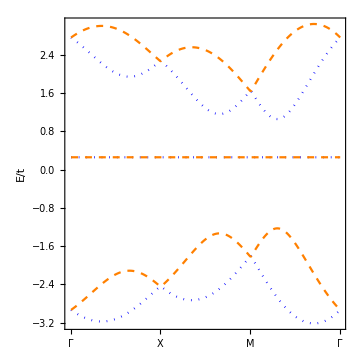

```mathematica
Block[ {λ={0.6,0.0},δ={0.0,0.0},ϵ=0.6,U=0.5, fil=3.0, β=100,krange=25},ListPlot[Table[ PlotMFDisp[bsp,U,fil,β,krange][[All,i]],{i,1,6,1}],PlotStyle->{{Blue,Dotted},{Orange,Dashed}},
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Mean-Field Magnetization

```mathematica
Clear[Magn];Magn[bsp_,U_, fil_,β_,krange_,orb_]:= Magn[bsp,U,fil,β,krange,orb]=  Module[{itr=ItrFnMF[bsp,U,fil,β,krange]},{1/2( itr[[4,orb]] + itr[[5,orb]]),1/(2I)( itr[[4,orb]] - itr[[5,orb]]), 1/2( itr[[2,orb]] - itr[[3,orb]])}];
```

```mathematica
Clear[Density];Density[bsp_,U_, fil_,β_,krange_]:= Density[bsp,U,fil,β,krange]=  Module[{itr=ItrFnMF[bsp,U,fil,β,krange]},Sum[ itr[[2,orb]] + itr[[3,orb]],{orb,1,3}]];
```

```mathematica
Block[ {λ={0.45,0},δ={0.0,0.0},ϵ=0.5,fil=3.0, β=100, krange=30},DiscretePlot[{Density[bsp,U,fil,β,krange],Norm[ Magn[bsp,U,fil,β,krange,1]],Norm[ Magn[bsp,U,fil,β,krange,2]],Norm[ Magn[bsp,U,fil,β,krange,3]]},{U,0,10},PlotRange->All]]
```

$Aborted

```mathematica
?Density
```

### Analytic Flat-band Wavefunction

```mathematica
mat2 = {{0,0,a, b, x,y},{0,0,bc, ac,yc,xc},{Conjugate[a],Conjugate[bc],0,0,0,0},{Conjugate[b],Conjugate[ac],0,0,0,0},{Conjugate[x],Conjugate[yc],0,0,0,0},{Conjugate[y],Conjugate[xc],0,0,0,0}};
```

```mathematica
Clear[waveF];waveF[λ_,δ_,k_] := waveF[λ,δ,k]=Normalize[ Module[{a =hamLieb[λ,δ,k] [[1,3]],b=hamLieb[λ,δ,k] [[1,4]],x =hamLieb[λ,δ,k] [[1,5]],y=hamLieb[λ,δ,k] [[1,6]]}, { 0,0,- Conjugate[b] x -  Conjugate[a] y,   - Conjugate[a] x +  Conjugate[b] y, 0,Conjugate[b]^2+ Conjugate[a]^2}]];
```

```mathematica
Clear[waveF2];waveF2[λ_,δ_,k_] := waveF2[λ,δ,k]=Normalize[ Module[{a =hamLieb[λ,δ,k] [[1,3]],b=hamLieb[λ,δ,k] [[1,4]],x =hamLieb[λ,δ,k] [[1,5]],y=hamLieb[λ,δ,k] [[1,6]]}, { 0,-x^2+y^2, 0,0,- x Conjugate[b] -  y Conjugate[a],  y Conjugate[b]+ x Conjugate[a] }]];
```

```mathematica
Block[ {λ=RandomReal[{0,1},2],δ=RandomReal[1,2],k=RandomReal[2π,2]}, hamLieb[λ,δ,k].waveF[λ,δ,k]]//MatrixForm//Chop
```

(0.169958-1.82003 ⅈ
0.214155-1.78597 ⅈ
0
0
0
0)

```mathematica
Block[ {λ=RandomReal[],δ=RandomReal[1,2],k=RandomReal[2π,2]}, hamLieb[λ,δ,k].waveF2[λ,δ,k]]//MatrixForm//Chop
```

(0
0
0
0
0
0)

```mathematica
Block[ {λ=0.6,δ={0.5,0.0},k=RandomReal[2π,2]}, hamLieb[λ,δ,k].(Normalize[waveF[λ,δ,k]+waveF2[λ,δ,k]])]//MatrixForm//Chop
```

(0
0
0
0
0
0)

```mathematica
TRO = KroneckerProduct[  IdentityMatrix[3],I  PauliMatrix[2]];
```

```mathematica
Block[ {λ=0.6,δ={0.5,0.0},k=RandomReal[2π,2]}, hamLieb[λ,δ,k].(TRO.Conjugate[Normalize[waveF[λ,δ,-k]+waveF2[λ,δ,-k]]])]//MatrixForm//Chop
```

(0
0
0
0
0
0)

### Wannier Functions

```mathematica
Clear[Psi];Psi[λ_,δ_,k_,band_]:= Psi[λ,δ,k,band]=Module[ {vec =Normalize[waveF[λ,δ,k]+ waveF2[λ,δ,k]], veck =Normalize[waveF[λ,δ,-k]+ waveF2[λ,δ,-k]]},  If[band==1, vec,TRO.Conjugate[veck] ]];
```

```mathematica
Psi[RandomReal[],RandomReal[1,2],RandomReal[2π,2],2]//MatrixForm
```

(-0.52648-0.305972 ⅈ
0.175574+0.0879716 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.626178-0.39227 ⅈ
0.188937+0.0946671 ⅈ)

```mathematica
Clear[WanFuPsi];WanFuPsi[λ_,δ_,r_,krange_,band_] := WanFuPsi[λ,δ,r,krange,band]=1/Length[kSpan[krange]] Sum[Exp[-I k.r]  Psi[λ,δ,k,band] ,{k,kSpan[krange]}]
```

now it’s amplitude

```mathematica
Clear[WFAmpPsi];WFAmpPsi[λ_,δ_,r_,krange_,band_] := WFAmpPsi[λ,δ,r,krange,band] =  Norm[WanFuPsi[λ,δ,r,krange,band]]^2;
```

```mathematica
Block[ {λ=0.5,δ={0.5,0.5},krange=50,band=1,r=τB}, WanFuPsi[λ,δ,r,krange,band]]//MatrixForm
```

(0.153645+0.144832 ⅈ
-0.629247+0.0804683 ⅈ
0.+0. ⅈ
0.+0. ⅈ
0.144832+0.153645 ⅈ
0.629247+0.0804683 ⅈ)

```mathematica
Block[ {λ=0.5,δ={0.5,0.5},krange=50,band=1},WFAmpPsi[λ,δ,{0,0},krange,band ]]//MatrixForm
```

0.894021

```mathematica
Clear[OmegaPsi];OmegaPsi[ λ_,δ_,range_,krange_,band_] := OmegaPsi[λ,δ,range,krange,band] =  Sum[ Norm[r]^2 WFAmpPsi[λ,δ,r,krange,band] ,{r,rSpan[range]}]- Norm[Sum[r  WFAmpPsi[λ,δ,r,krange,band] ,{r,rSpan[range]}]]^2;
```

#### Wannier Checks

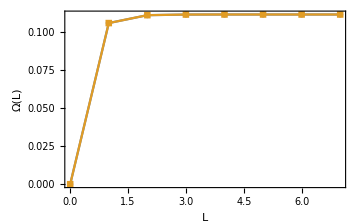

```mathematica
Block[ {λ=0.5,δ={0.5,0.5},krange=50,band=1},DiscretePlot[ {OmegaPsi[λ,δ,range,krange,1],OmegaPsi[λ,δ,range,krange,2]}, {range,0,7}, FrameLabel->{"L","Ω(L)"},PlotMarkers->Automatic] ]
```

Not much difference between spatial structure of 1 and 2

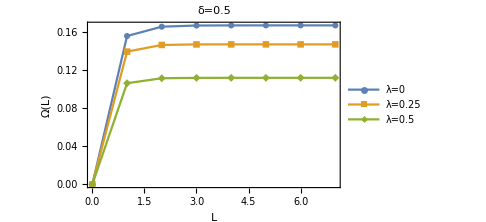

```mathematica
Block[ {λ=0.25,δ={0.5,0.5},krange=50,band=1},DiscretePlot[ {OmegaPsi[0.0,δ,range,krange,1],OmegaPsi[λ,δ,range,krange,1],OmegaPsi[2 λ,δ,range,krange,1]}, {range,0,7}, FrameLabel->{"L","Ω(L)"},PlotMarkers->Automatic,PlotLegends->{"λ=0","λ=0.25","λ=0.5"},PlotLabel->"δ=0.5"] ]
```

Now let us look at structure of Wannier Function

```mathematica
Block[ {λ=0.25,δ={0.5,0.5},krange=50,r={0,0},band=1},WanFuPsi[λ,δ,r,krange,band]]//MatrixForm//Chop
```

(0.0915486+0.0834593 ⅈ
-0.643612+0.0244047 ⅈ
0
0
0.0834593+0.0915486 ⅈ
0.643612+0.0244047 ⅈ)

```mathematica
Block[ {λ=0.25,δ={0.5,0.5},krange=50,r={0,0},band=2},WanFuPsi[λ,δ,r,krange,band]]//MatrixForm//Chop
```

(-0.643612-0.0244047 ⅈ
-0.0915486+0.0834593 ⅈ
0
0
0.643612-0.0244047 ⅈ
-0.0834593+0.0915486 ⅈ)

### Projected Interactions

```mathematica
Clear[ProjIntNN];ProjIntNN[λ_,δ_,r_,l_,krange_,range_]:=ProjIntNN[λ,δ,r,l,krange,range] = Module[ {l1 = l[[1]], l2 = l[[2]], l3 = l[[3]], l4 = l[[4]]}, Sum[Sum[ Conjugate[WanFuPsi[λ,δ,-rS,krange,l1][[α]]]WanFuPsi[λ,δ,-rS,krange,l2][[α]] Conjugate[WanFuPsi[λ,δ,r-rS,krange,l3][[α+1]]]WanFuPsi[λ,δ,r-rS,krange,l4][[α+1]],{α,1,6,2}],{rS,rSpan[range]}]]
```

```mathematica
Clear[ProjIntSF];ProjIntSF[λ_,δ_,r_,l_,krange_,range_]:=ProjIntSF[λ,δ,r,l,krange,range] = Module[ {l1 = l[[1]], l2 = l[[2]], l3 = l[[3]], l4 = l[[4]]}, Sum[Sum[ Conjugate[WanFuPsi[λ,δ,-rS,krange,l1][[α]]]WanFuPsi[λ,δ,-rS,krange,l2][[α+1]] WanFuPsi[λ,δ,r-rS,krange,l3][[α]]Conjugate[WanFuPsi[λ,δ,r-rS,krange,l4][[α+1]]],{α,1,6,2}],{rS,rSpan[range]}]]
```

```mathematica
Clear[ProjIntPH];ProjIntPH[λ_,δ_,r_,l_,krange_,range_]:=ProjIntPH[λ,δ,r,l,krange,range] = Module[ {l1 = l[[1]], l2 = l[[2]], l3 = l[[3]], l4 = l[[4]]}, Sum[Sum[ Conjugate[WanFuPsi[λ,δ,-rS,krange,l1][[α]]]Conjugate[WanFuPsi[λ,δ,-rS,krange,l2][[α+1]] ]WanFuPsi[λ,δ,r-rS,krange,l3][[α+1]]WanFuPsi[λ,δ,r-rS,krange,l4][[α]],{α,1,6,2}],{rS,rSpan[range]}]]
```

#### On-site Hubbard

```mathematica
Block[ {λ=0.0,δ={0.5,0.5}, r={0,0}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntNN[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 2 | 0
1 | 1 | 2 | 1 | 0
1 | 1 | 2 | 2 | 0
1 | 2 | 1 | 1 | 0
1 | 2 | 1 | 2 | 0
1 | 2 | 2 | 1 | 0
1 | 2 | 2 | 2 | 0
2 | 1 | 1 | 1 | 0
2 | 1 | 1 | 2 | 0
2 | 1 | 2 | 1 | 0
2 | 1 | 2 | 2 | 0
2 | 2 | 1 | 1 | 0.361899
2 | 2 | 1 | 2 | 0
2 | 2 | 2 | 1 | 0
2 | 2 | 2 | 2 | 0)

#### Nearest Neighbor

```mathematica
λ=0.2;
```

```mathematica
Block[ {δ={0.5,0.5}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntNN[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.00074975
1 | 1 | 1 | 2 | 0.0000282629+0.0000810675 ⅈ
1 | 1 | 2 | 1 | 0.0000282629-0.0000810675 ⅈ
1 | 1 | 2 | 2 | 0.0000350069
1 | 2 | 1 | 1 | -0.00202223+0.00146729 ⅈ
1 | 2 | 1 | 2 | -0.000475823+0.0000687614 ⅈ
1 | 2 | 2 | 1 | -0.00014371+0.000487966 ⅈ
1 | 2 | 2 | 2 | 0.0000152577-0.0000406503 ⅈ
2 | 1 | 1 | 1 | -0.00202223-0.00146729 ⅈ
2 | 1 | 1 | 2 | -0.00014371-0.000487966 ⅈ
2 | 1 | 2 | 1 | -0.000475823-0.0000687614 ⅈ
2 | 1 | 2 | 2 | 0.0000152577+0.0000406503 ⅈ
2 | 2 | 1 | 1 | 0.027912
2 | 2 | 1 | 2 | 0.00204922+0.00233598 ⅈ
2 | 2 | 2 | 1 | 0.00204922-0.00233598 ⅈ
2 | 2 | 2 | 2 | 0.001347)

```mathematica
Block[ {δ={0.5,0.2}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntNN[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.000836984
1 | 1 | 1 | 2 | -7.0433×10^-6+0.0000467884 ⅈ
1 | 1 | 2 | 1 | -7.0433×10^-6-0.0000467884 ⅈ
1 | 1 | 2 | 2 | 0.0000217922
1 | 2 | 1 | 1 | -0.00140838+0.000248645 ⅈ
1 | 2 | 1 | 2 | -0.000240876+0.00016821 ⅈ
1 | 2 | 2 | 1 | -0.000165389+0.000343656 ⅈ
1 | 2 | 2 | 2 | 0.0000595931-0.000118942 ⅈ
2 | 1 | 1 | 1 | -0.00140838-0.000248645 ⅈ
2 | 1 | 1 | 2 | -0.000165389-0.000343656 ⅈ
2 | 1 | 2 | 1 | -0.000240876-0.00016821 ⅈ
2 | 1 | 2 | 2 | 0.0000595931+0.000118942 ⅈ
2 | 2 | 1 | 1 | 0.056911
2 | 2 | 1 | 2 | 0.00103363+0.00217027 ⅈ
2 | 2 | 2 | 1 | 0.00103363-0.00217027 ⅈ
2 | 2 | 2 | 2 | 0.00166441)

```mathematica
Block[ {δ={0.5,0.2}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntSF[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.000164701-0.000350599 ⅈ
1 | 1 | 1 | 2 | 0.0000691506-0.000110677 ⅈ
1 | 1 | 2 | 1 | -0.00125397+0.000381816 ⅈ
1 | 1 | 2 | 2 | -0.000164701+0.000350599 ⅈ
1 | 2 | 1 | 1 | -0.0000321467+0.0000187838 ⅈ
1 | 2 | 1 | 2 | 6.64395×10^-6+0.0000132593 ⅈ
1 | 2 | 2 | 1 | 0.000252444+0.000755318 ⅈ
1 | 2 | 2 | 2 | 0.0000321467-0.0000187838 ⅈ
2 | 1 | 1 | 1 | -0.00080641+0.00228371 ⅈ
2 | 1 | 1 | 2 | 0.00130328+0.000508249 ⅈ
2 | 1 | 2 | 1 | 0.0568661-0.00120367 ⅈ
2 | 1 | 2 | 2 | 0.00080641-0.00228371 ⅈ
2 | 2 | 1 | 1 | -0.000164701+0.000350599 ⅈ
2 | 2 | 1 | 2 | -0.0000691506+0.000110677 ⅈ
2 | 2 | 2 | 1 | 0.00125397-0.000381816 ⅈ
2 | 2 | 2 | 2 | 0.000164701-0.000350599 ⅈ)

```mathematica
Block[ {δ={0.5,0.2}, r={0,1}, krange=50,range=3}, Flatten[Table[ {l1,l2,l3,l4,ProjIntPH[λ,δ,r,{l1,l2,l3,l4},krange,range]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0.000165389-0.000343656 ⅈ
1 | 1 | 1 | 2 | -0.00140838+0.000248645 ⅈ
1 | 1 | 2 | 1 | -0.0000595931+0.000118942 ⅈ
1 | 1 | 2 | 2 | -0.000240876+0.00016821 ⅈ
1 | 2 | 1 | 1 | -7.0433×10^-6-0.0000467884 ⅈ
1 | 2 | 1 | 2 | -0.000836984
1 | 2 | 2 | 1 | 0.0000217922
1 | 2 | 2 | 2 | 7.0433×10^-6-0.0000467884 ⅈ
2 | 1 | 1 | 1 | -0.00103363+0.00217027 ⅈ
2 | 1 | 1 | 2 | 0.056911
2 | 1 | 2 | 1 | -0.00166441
2 | 1 | 2 | 2 | 0.00103363+0.00217027 ⅈ
2 | 2 | 1 | 1 | -0.000240876-0.00016821 ⅈ
2 | 2 | 1 | 2 | 0.00140838+0.000248645 ⅈ
2 | 2 | 2 | 1 | 0.0000595931+0.000118942 ⅈ
2 | 2 | 2 | 2 | 0.000165389+0.000343656 ⅈ)

#### Fermionic det

```mathematica
FDet[l_]:= Det[ {{l[[1]], l[[2]], l[[3]], l[[4]]},{l[[2]], l[[3]], l[[4]], l[[1]]},{l[[3]], l[[4]], l[[1]], l[[2]]},{l[[4]], l[[1]], l[[2]], l[[3]]}}];
```

```mathematica
Flatten[Table[ {l1,l2,l3,l4,Sign[FDet[{l1,l2,l3,l4}]]},{l1,1,2},{l2,1,2},{l3,1,2},{l4,1,2}],3]//MatrixForm//Chop
```

(1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 2 | 1
1 | 1 | 2 | 1 | -1
1 | 1 | 2 | 2 | 0
1 | 2 | 1 | 1 | 1
1 | 2 | 1 | 2 | 0
1 | 2 | 2 | 1 | 0
1 | 2 | 2 | 2 | 1
2 | 1 | 1 | 1 | -1
2 | 1 | 1 | 2 | 0
2 | 1 | 2 | 1 | 0
2 | 1 | 2 | 2 | -1
2 | 2 | 1 | 1 | 0
2 | 2 | 1 | 2 | 1
2 | 2 | 2 | 1 | -1
2 | 2 | 2 | 2 | 0)

#### Detail layout

Density-Density channel

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={1,0}, krange=50,range=3}, {ProjIntNN[λ,δ,r,{1,1,1,1},krange,range],ProjIntNN[λ,δ,r,{2,2,2,2},krange,range],ProjIntNN[λ,δ,r,{1,1,2,2},krange,range],ProjIntNN[λ,δ,r,{2,2,1,1},krange,range]}]//MatrixForm//Chop
```

(0.00074975
0.001347
0.0000350069
0.027912)

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={-1,0}, krange=50,range=3}, {ProjIntNN[λ,δ,r,{1,1,1,1},krange,range],ProjIntNN[λ,δ,r,{2,2,2,2},krange,range],ProjIntNN[λ,δ,r,{1,1,2,2},krange,range],ProjIntNN[λ,δ,r,{2,2,1,1},krange,range]}]//MatrixForm//Chop
```

(0.001347
0.00074975
0.0000350069
0.027912)

Spin flip-Spin flip channel

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={-1,0}, krange=50,range=3}, {ProjIntSF[λ,δ,r,{1,2,1,2},krange,range],ProjIntSF[λ,δ,r,{1,2,2,1},krange,range],ProjIntSF[λ,δ,r,{2,1,1,2},krange,range],ProjIntSF[λ,δ,r,{2,1,2,1},krange,range]}]//MatrixForm//Chop
```

(-8.84664×10^-6+0.000018777 ⅈ
-0.000802558-0.000497146 ⅈ
-6.1693×10^-6-0.000737043 ⅈ
0.0277186-0.00200912 ⅈ)

```mathematica
Block[ {λ=0.2,δ={0.5,0.5}, r={1,0}, krange=50,range=3}, {ProjIntSF[λ,δ,r,{1,2,1,2},krange,range],ProjIntSF[λ,δ,r,{1,2,2,1},krange,range],ProjIntSF[λ,δ,r,{2,1,1,2},krange,range],ProjIntSF[λ,δ,r,{2,1,2,1},krange,range]}]//MatrixForm//Chop
```

(-8.84664×10^-6-0.000018777 ⅈ
-6.1693×10^-6+0.000737043 ⅈ
-0.000802558+0.000497146 ⅈ
0.0277186+0.00200912 ⅈ)

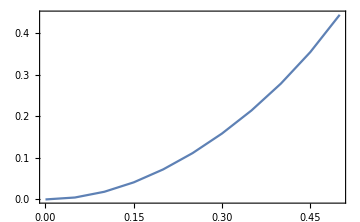

```mathematica
Block[ {δ={0.5,0.5}, r={1,0}, krange=50,range=3},DiscretePlot[ Abs[ProjIntSF[λ,δ,r,{2,1,2,1},krange,range]-ProjIntNN[λ,δ,r,{2,2,1,1},krange,range]]/ProjIntNN[λ,δ,r,{2,2,1,1},krange,range],{λ,0.,0.5,0.05},PlotLegends->Automatic]]
```

```mathematica
Block[ {λ=0.0,δ=0.5, r={1,0}, krange=50,range=3},DiscretePlot[ Abs[ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{1,0},{2,1,2,1},krange,range]-ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{0,1},{2,2,1,1},krange,range]]/ProjIntNN[λ,δ,r,{2,2,1,1},krange,range],{θ,0.,2π,0.1},PlotLegends->Automatic]]
```

$Aborted

```mathematica
Block[ {λ=0.2,δ=0.5, r={1,0}, krange=50,range=3},DiscretePlot[ Abs[ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{1,0},{2,1,2,1},krange,range]-ProjIntNN[λ,δ{Cos[θ],Sin[θ]},{0,1},{2,2,1,1},krange,range]]/ProjIntNN[λ,δ,r,{2,2,1,1},krange,range],{θ,0.,2π,0.1},PlotLegends->Automatic]]
```